```mathematica
a[1]=Import["D:\\作業中\\dataset\\データセット\\dyrskjot\\memo\\dyrskjot.txt","Table"];
```

```mathematica
Dimensions[a[1]]
```

{43}

```mathematica
a[1][[1]][[1]]
```

A28102_at

```mathematica
a[1][[2]][[3]]
```

c

```mathematica
a[1][[3]]
```

{class,meta}

```mathematica
Dimensions[a[1][[4]]]
```

{5726}

```mathematica
a[1][[2]]//Length
```

5726

```mathematica
Table[a[1][[i]][[1]],{i,1,10}]
```

{A28102_at,c,class,24.4,24.8,1.5,15.4,45.9,-18.2,10}

```mathematica
Table[a[1][[i]][[1]],{i,1,10}]
Table[a[1][[2]][[i]],{i,1,10}]
Table[a[1][[3]][[i]],{i,1,10}]
```

{A28102_at,c,class,24.4,24.8,1.5,15.4,45.9,-18.2,10}

{c,c,c,c,c,c,c,c,c,c}

Part::partw: {class,meta}の部分3は存在しません．

Part::partw: {class,meta}の部分4は存在しません．

Part::partw: {class,meta}の部分5は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

{class,meta,{class,meta}⟦3⟧,{class,meta}⟦4⟧,{class,meta}⟦5⟧,{class,meta}⟦6⟧,{class,meta}⟦7⟧,{class,meta}⟦8⟧,{class,meta}⟦9⟧,{class,meta}⟦10⟧}

```mathematica
Table[a[1][[j]][[22284]],{j,4,55}]
```

Part::partw: {24.4,10.5,30.4,30.8,66,94.1,109.3,361.8,10.5,121.7,-40.4,103,11.3,7.9,-4,2.5,15.9,165.1,75.9,-29.5,91.5,207.6,89.9,355.3,21.4,30.5,125.9,340.5,-1.5,3934,49.8,546.5,122.7,230.9,83.1,287.1,-2.2,107.6,64.9,441.4,34.5,-12.1,65.3,111.5,25.9,0.3,-8.5,-28.7,371.1,2341.2,«5676»}の部分22284は存在しません．

Part::partw: {24.8,29.9,65.1,174.4,40.4,26.2,46.6,362.6,28.5,116.5,-32.4,293.6,831.9,-3.1,10.2,3.8,30.7,79.3,407.4,32,97.5,195.3,61.2,304.3,27.5,0.2,135,928.2,31.4,3688.6,199.3,314.9,69.5,268.1,35.4,231.1,-17.6,161.1,300.7,647.2,44.2,-6.6,70.3,225.3,37.3,-6.8,8.1,254.4,81.7,835.6,«5676»}の部分22284は存在しません．

Part::partw: {1.5,8.5,66.5,255.7,118.9,80.6,68.4,310.5,10.7,71.9,-52.1,364.7,491.9,-1.1,-9.9,-0.6,7.1,158.7,151.7,2.9,158.7,55.5,141.3,157.1,18.7,11.3,317.4,597.5,42.8,1009.2,101.8,652.6,346.6,347.6,107.4,268.6,-2.8,90.8,11.2,524.1,32.6,-0.6,28.3,71.7,23.1,-2.6,19.6,349.1,106.6,657.5,«5676»}の部分22284は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

{{24.4,10.5,30.4,30.8,66,94.1,109.3,361.8,10.5,121.7,-40.4,103,11.3,7.9,-4,2.5,15.9,165.1,75.9,-29.5,91.5,207.6,89.9,355.3,21.4,5676,60.6,-43.8,13.4,-4.8,-10,6.6,5.5,-15.1,108.2,1.7,14.7,5.5,-4,389.9,-41.2,1798.1,110.6,275.3,36.9,10,5,308.1,101.1,T2+,1032-1}⟦22284⟧,50,1}
 |  |  |  |

```mathematica
Dimensions[Drop[a[1][[4]],-3]]
```

{5723}

```mathematica
a[1]//Dimensions
```

{43}

```mathematica
data0=Transpose[Drop[Transpose[Table[a[1][[j]],{j,4,43}]],-2]];
```

```mathematica
Dimensions[data0]
```

{40,5724}

```mathematica
data0//Total//Total
```

5.82409×10^7

```mathematica
{n[0],p}=Dimensions[data0]
```

{40,5724}

```mathematica
classnum=3;
```

```mathematica
label={"T2+","Ta","T1"};
```

```mathematica
For[i=1,i≤ 3,i++,l[i]={}]
```

```mathematica
Table[a[1][[i]][[5725]],{i,4,43}]
```

{T2+,T2+,Ta,Ta,T2+,T2+,Ta,T2+,T2+,Ta,T2+,Ta,Ta,Ta,T1,Ta,Ta,Ta,Ta,T1,T1,T2+,Ta,T1,T1,Ta,Ta,Ta,T2+,Ta,Ta,Ta,Ta,T2+,T1,T1,T1,T1,T1,T1}

```mathematica
For[i=1,i≤ 3,i++,
l[i]=Flatten[
Table[
If[
a[1][[j]][[5725]]==label[[i]],
Join[l[i],{j-3}],
Join[l[i],{}]
],{j,4,43}]]
]
```

```mathematica
l[1]
l[2]
l[3]
```

{1,2,5,6,8,9,11,22,29,34}

{3,4,7,10,12,13,14,16,17,18,19,23,26,27,28,30,31,32,33}

{15,20,21,24,25,35,36,37,38,39,40}

```mathematica
Dimensions[l[1]]
Dimensions[l[2]]
Dimensions[l[3]]
```

{10}

{19}

{11}

```mathematica
{n[0],p}=Dimensions[data0]
```

{40,5724}

```mathematica
classnum=3;
```

```mathematica
For[i=1,i≤ classnum,i++,n[i]=Length[l[i]]];
For[i=1,i≤ classnum,i++,x[i]=data0[[l[i]]]];
For[i=1,i≤ classnum,i++,m[i]=N[Mean[x[i]]]];
For[i=1,i≤ classnum,i++,s[i]=N[Sum[Norm[x[i][[j]]-m[i]]^2,{j,1,n[i]}]/(n[i]-1)]];
```

```mathematica
Table[s[i],{i,1,classnum}]
```

{5.6996×10^8,1.95176×10^8,4.10014×10^8}

```mathematica
Table[n[i],{i,1,classnum}]
```

{10,19,11}

```mathematica
Do[V[pi]=x[pi],{pi,1,classnum}]
γ[a_]:=(a^-1 Log[a])^(1/2)
```

```mathematica
Do[n[pi]=Length[V[pi]];
mean[pi]=Mean[V[pi]];SD[pi]=(V[pi]-Table[mean[pi],n[pi]]).Transpose[V[pi]-Table[mean[pi],n[pi]]]/(n[pi]-1);
{val[pi],vec[pi]}=Eigensystem[SD[pi]];
(*Noise Reduction Methodology*)
Do[NRVal[pi,i]=val[pi][[i]]-(Tr[SD[pi]]-Sum[val[pi][[l]],{l,1,i}])/(n[pi]-1-i);
NRVec[pi,i]=((n[pi]-1)NRVal[pi,i])^(-1/2)Transpose[V[pi]-Table[mean[pi],n[pi]]].vec[pi][[i]]
,{i,1,n[pi]-2}];
(*Cross Data Methodology*)
n[pi,1]=Ceiling[n[pi]/2];n[pi,2]=n[pi]-n[pi,1];CrossData[pi,1]=Take[V[pi],n[pi,1]];CrossData[pi,2]=Take[V[pi],-n[pi,2]];
Do[CrossMean[pi,i]=Mean[CrossData[pi,i]],{i,1,2}];
SDCross[pi]=(CrossData[pi,1]-Table[CrossMean[pi,1],{n[pi,1]}]).Transpose[CrossData[pi,2]-Table[CrossMean[pi,2],{n[pi,2]}]]/((n[pi,1]-1)(n[pi,2]-1))^(1/2);
SDCross2[pi]=SDCross[pi].Transpose[SDCross[pi]];
{SDVal2[pi],SDVec[pi]}=Eigensystem[SDCross2[pi]];
SDVal[pi]=SDVal2[pi]//Sqrt;
Ψ[pi,1]=Tr[SDCross2[pi]];
Do[Ψ[pi,i]=Tr[SDCross2[pi]]-Sum[SDVal2[pi][[j]],{j,1,i-1}],{i,2,n[pi,2]}];
Do[ϵ[pi,i]=NRVal[pi,i]/Tr[SD[pi]];η[pi,i]=(SDVal2[pi][[i]])/Ψ[pi,i];τ[pi,i]=(*1-(SDVal2[pi][[i]])/Ψ[pi,i]*)Ψ[pi,i+1]/Ψ[pi,i],{i,1,n[pi,2]-1}];
khat[pi]=Min[{Min[Table[If[τ[pi,r+1](1+(r+1)γ[n[pi]])>1,r,Infinity],{r,1,n[pi,2]-2}]],n[pi,2]}]
,{pi,1,classnum}]
```

```mathematica
Do[
Print["ϵ"pi];
Print[Table[ϵ[pi,i],{i,1,n[pi,2]-2}]];
Print["η"pi];
Print[Table[η[pi,i],{i,1,n[pi,2]-2}]];
,{pi,1,classnum}]
```

ϵ

{0.201417,0.184886,0.0881102}

η

{0.757775,0.890292,0.946289}

2 ϵ

{0.50891,0.0701399,0.0383178,0.0289962,0.0244942,0.0172493,0.0168481}

2 η

{0.974617,0.871445,0.472495,0.396983,0.562564,0.926597,0.977168}

3 ϵ

{0.230687,0.0841106,0.0487992}

3 η

{0.712642,0.938661,0.772214}

```mathematica
Do[Print[khat[pi]],{pi,1,classnum}]
```

5

2

5

```mathematica
(*Rounded*)
```

```mathematica
Do[
Print["ϵ"pi];
Print[Table[Round[1000*ϵ[pi,i]]/1000//N,{i,1,n[pi,1]-1}]];
Print["η"pi];
Print[Table[Round[1000*η[pi,i]]/1000//N,{i,1,n[pi,1]-1}]];
,{pi,1,classnum}]
```

ϵ

{0.201,0.185,0.088,0.056}

η

{0.758,0.89,0.946,1.}

2 ϵ

{0.509,0.07,0.038,0.029,0.024,0.017,0.017,0.012,0.001 Round[1000. ϵ[2.,9.]]}

2 η

{0.975,0.871,0.472,0.397,0.563,0.927,0.977,1.,0.001 Round[1000. η[2.,9.]]}

3 ϵ

{0.231,0.084,0.049,0.042,0.001 Round[1000. ϵ[3.,5.]]}

3 η

{0.713,0.939,0.772,1.,0.001 Round[1000. η[3.,5.]]}

```mathematica
ddimpoliminalKernel[x1_,x2_,dim_]:=(1+x1.x2)^dim
gaussKernel[x1_,x2_,sigma_]:=Exp[-Norm[x1-x2]^2 /(sigma)]
exponetialKernel[x1_,x2_,beta_]:=Exp[ x1.x2/beta]
laplaceKernel[x1_,x2_,alpha_]:=Exp[- Norm[x1-x2,1]/alpha]
```

```mathematica
Do[V[i]=x[i],{i,1,3}]
```

```mathematica
V[1]vs. V[2]
```

$Aborted[]

```mathematica
de[V1_,V2_,ms1_,ms2_]:=Module[{a},
mm[1]=ms1;mm[2]=ms2;mm[0]=Sum[mm[i],{i,1,2}];
one=IdentityMatrix[mm[0]]-Table[1/mm[0],{i,1,mm[0]},{j,1,mm[0]}];
x[1]= Take[V1,{1,mm[1]}];x[2]= Take[V2,{1,mm[2]}];
x[0]=Join[x[1],x[2]];trS = Variance[x[0]]//Total;
gram[1]=Table[x[0][[i]].x[0][[j]],{i,1,mm[0]},{j,1,mm[0]}];
gamma = trS;
Do[gram[2,k]=Table[gaussKernel[x[0][[i]],x[0][[j]],gamma^((3k-1)/5)],{i,1,mm[0]},{j,1,mm[0]}],{k,1,3}];
gm[1]=one.gram[1].one;Do[gm[2,k]=one.gram[2,k].one,{k,1,3}];
ev[1]=Eigensystem[gm[1]];Do[ev[2,k]=Eigensystem[gm[2,k]],{k,1,3}];
Print["Linear"];
range=2.5;
plot[1]=Table[√mm[0]{ev[1][[2,1,j]],ev[1][[2,2,j]]},{j,1,mm[0]}];
Print[Show[
ListPlot[Take[plot[1],{1,mm[1]}],PlotMarkers->{"●",Medium},PlotStyle->Red],
ListPlot[Take[plot[1],{mm[1]+1,mm[0]}],PlotMarkers->{"▲",Large},PlotStyle->Lighter[Blue]],
PlotRange->{{-range,range},{-range,range}},AxesOrigin->{0,0},Axes-> True,AxesLabel-> {"z_(1  j)","z_(2j)"},AspectRatio->1]];
Print["Gausssian"];
range=2.5;
Table[
plot[2,k]=Table[√mm[0]{ev[2,k][[2,1,j]],ev[2,k][[2,2,j]]},{j,1,mm[0]}];
Show[
ListPlot[Take[plot[2,k],{1,mm[1]}],PlotMarkers->{"●",Medium},PlotStyle->Red],
ListPlot[Take[plot[2,k],{mm[1]+1,mm[0]}],PlotMarkers->{"▲",Large},PlotStyle->Lighter[Blue]],
PlotRange->{{-range,range},{-range,range}},AxesOrigin->{0,0},Axes-> True,AxesLabel-> {"z_(1  j)","z_(2j)"},AspectRatio->1]
,{k,1,3}]
]
```

```mathematica
Table[n[i],{i,1,3}]
```

{10,19,11}

Linear

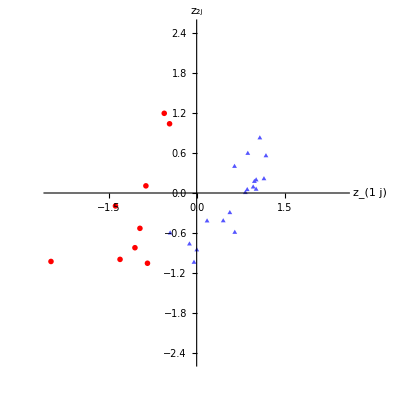

Gausssian

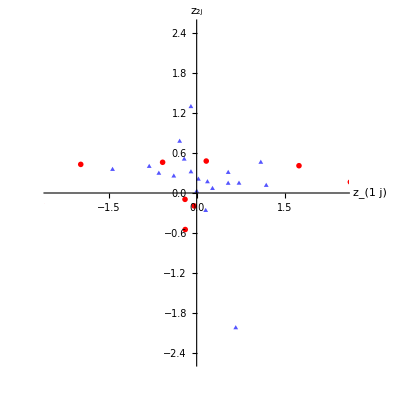
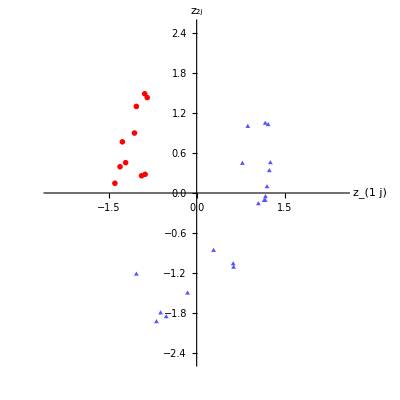
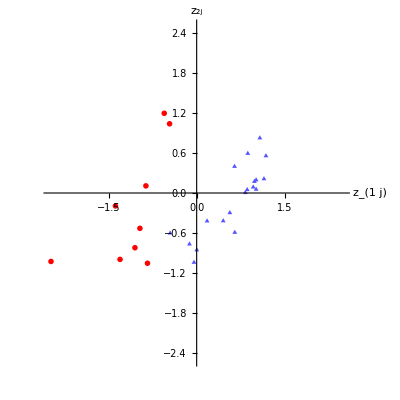

```mathematica
de[V[1],V[2],10,19]
```

Linear

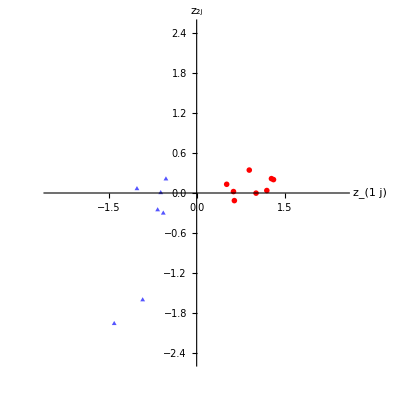

Gausssian

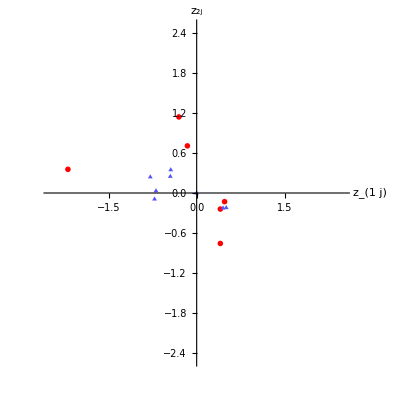
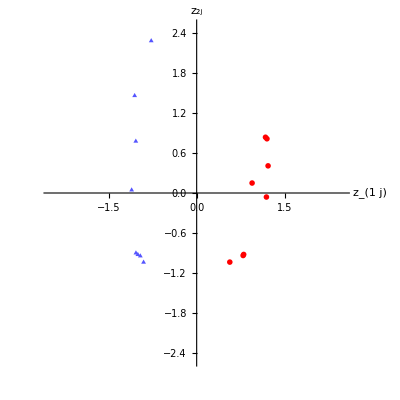
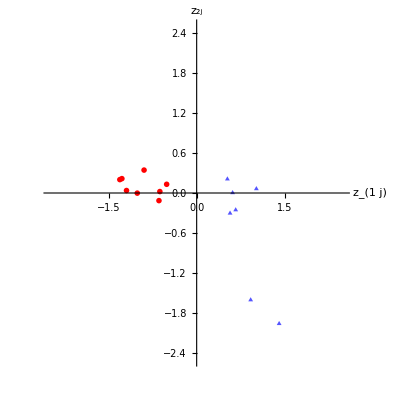

```mathematica
de[V[2],V[3],8,8]
```

```mathematica
de3[ms1_,ms2_,ms3_]:=Module[{a},
mm[1]=ms1;mm[2]=ms2;mm[3]=ms3;mm[0]=Sum[mm[i],{i,1,3}];
one=IdentityMatrix[mm[0]]-Table[1/mm[0],{i,1,mm[0]},{j,1,mm[0]}];
x[1]= Take[V[1],{1,mm[1]}];x[2]= Take[V[2],{1,mm[2]}];
x[3]= Take[V[3],{1,mm[3]}];
x[0]=Join[x[1],x[2],x[3]];trS = Variance[x[0]]//Total;
gram[1]=Table[x[0][[i]].x[0][[j]],{i,1,mm[0]},{j,1,mm[0]}];
gamma = trS;
Do[gram[2,k]=Table[gaussKernel[x[0][[i]],x[0][[j]],gamma^((3k-1)/5)],{i,1,mm[0]},{j,1,mm[0]}],{k,1,3}];
gm[1]=one.gram[1].one;Do[gm[2,k]=one.gram[2,k].one,{k,1,3}];
ev[1]=Eigensystem[gm[1]];Do[ev[2,k]=Eigensystem[gm[2,k]],{k,1,3}];
Print["Linear"];
range=2.5;
plot[1]=Table[√mm[0]{ev[1][[2,1,j]],ev[1][[2,2,j]]},{j,1,mm[0]}];
Print[Show[
ListPlot[Take[plot[1],{1,mm[1]}],PlotMarkers->{"●",Medium},PlotStyle->Red],
ListPlot[Take[plot[1],{mm[1]+1,mm[1]+mm[2]}],PlotMarkers->{"▲",Large},PlotStyle->Lighter[Blue]],
ListPlot[Take[plot[1],{mm[1]+mm[2]+1,mm[0]}],PlotMarkers->{"◆",Large},PlotStyle->Darker[Green]],
PlotRange->{{-range,range},{-range,range}},AxesOrigin->{0,0},Axes-> True,AxesLabel-> {"z_(1  j)","z_(2j)"},AspectRatio->1]];
Print["Gausssian"];
range=2.5;
Table[
plot[2,k]=Table[√mm[0]{ev[2,k][[2,1,j]],ev[2,k][[2,2,j]]},{j,1,mm[0]}];
Show[
ListPlot[Take[plot[2,k],{1,mm[1]}],PlotMarkers->{"●",Medium},PlotStyle->Red],
ListPlot[Take[plot[1],{mm[1]+1,mm[1]+mm[2]}],PlotMarkers->{"▲",Large},PlotStyle->Lighter[Blue]],
ListPlot[Take[plot[1],{mm[1]+mm[2]+1,mm[0]}],PlotMarkers->{"◆",Large},PlotStyle->Darker[Green]],
PlotRange->{{-range,range},{-range,range}},AxesOrigin->{0,0},Axes-> True,AxesLabel-> {"z_(1  j)","z_(2j)"},AspectRatio->1]
,{k,1,3}]
]
```

Linear

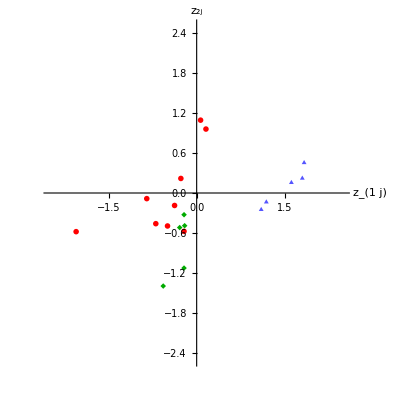

Gausssian

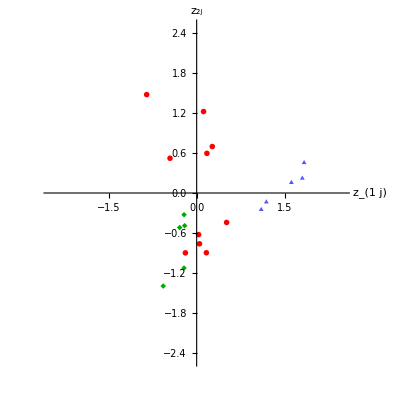
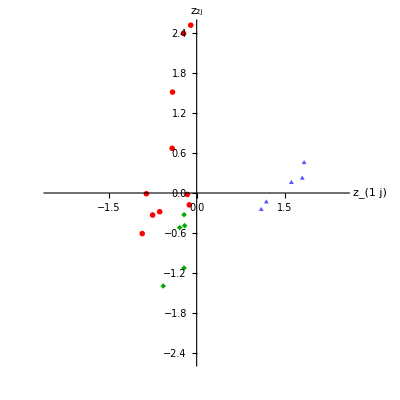
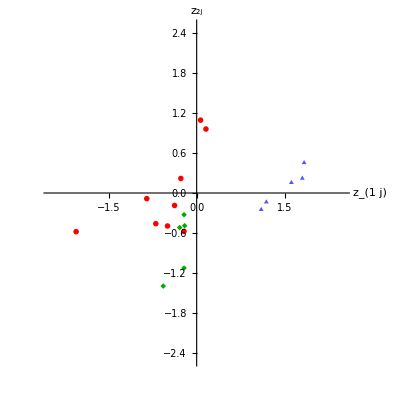

```mathematica
de3[10,5,5]
```

Linear

-Graphics-

Gausssian

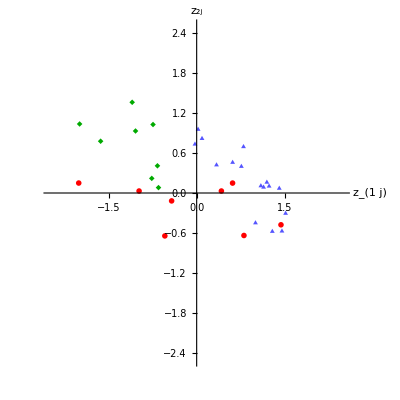
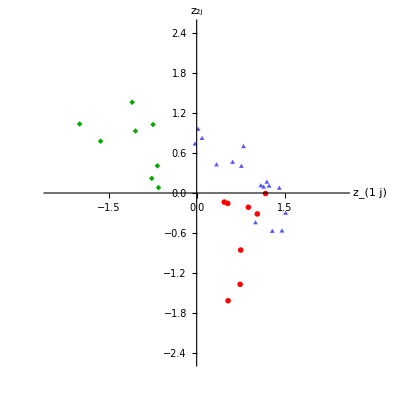
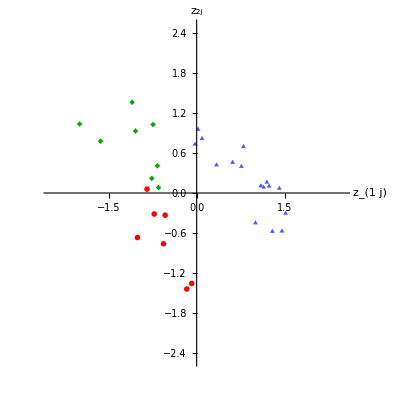

```mathematica
de3[8,16,8]
```